# Quiver Yangian Demo

```mathematica
Print[NotebookDirectory[]]
```

/Users/bpioline/tex/wallcrossing/QuiverYangian/math/

```mathematica
SetDirectory[NotebookDirectory[]];
<<CoulombHiggs`
```

CoulombHiggs 6.0 - A package for evaluating quiver invariants

Computes NCDT invariants for brane tilings following Mozgovoy Reineke 0809.0117 and Li Yamazaki 2003.08909 
hMat[[i,j,m]] is the weight of the m-th arrow from i to j, subject to vertex and relaxed loop constraints

```mathematica
ListKnownBraneTilings
```

1:C^3

2:Conifold=Y10

3:C^2xC/2

4:C^2xC/3

5:C^3/2x2

6:SPP=L121

7:L131

8:P2=C^3/(1,1,1)

9:F0.1=P1xP1

10:F0.2=P1xP1

11:F1=dP1=Y21=L312

12:F2=C^3/(1,1,2)

13:dP2.1

14:dP2.2

15:dP3.1

16:dP3.2

17:dP3.3

18:dP3.4

19:PdP2

20:PdP3a=C^3/(1,2,3)

21:PdP3b

22:PdP3c=SPP/2

23:PdP4a

24:PdP4b

25:PdP5a=Conifold/2x2

26:PdP5b=L131/2

27:PdP5c=C3/4x2

28:PdP6=C3/3x3

29:L152

30:Y32=L153

31:C^3/(1,1,3)

32:C^3/(1,1,4)

```mathematica
$QuiverVertexLabels={};{Tiling,Fan,hMat,Wp,Wm,v1,v2}=BraneTilingsData[[10]];Tiling
```

F0.2=P1xP1

```mathematica
(* label vertices from 0 to K-1 *) 
$QuiverVertexLabels=Range[0,Length[hMat]-1];
```

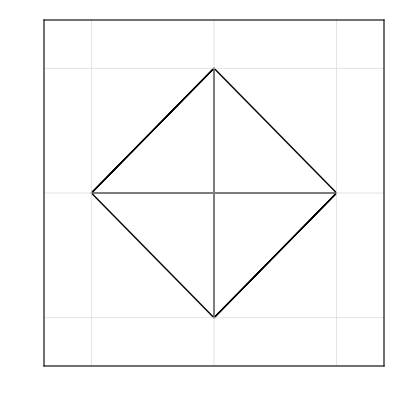
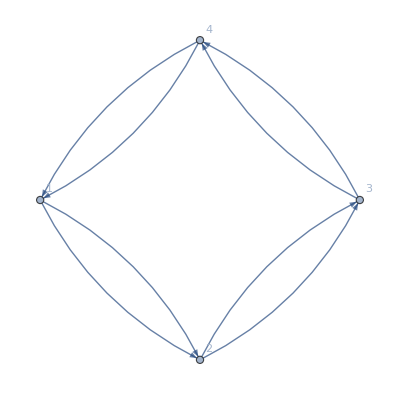
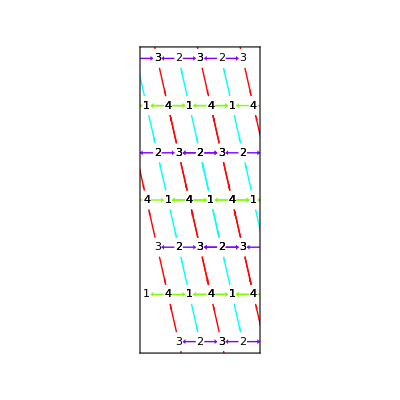

```mathematica
L=2.7;{PlotToricFan[Fan],PlotQuiver[hMat],PlotTiling[hMat,8,{v1,v2},{{-L-.5,L-.5},{-L,L}},.2]}
```

```mathematica
(* recompute height matrix such that h(Phi_{1,2}^1)=h1, h(Phi_{2,3}^1)=h2 *)
hMat=HeightMatrixFromPotential[Wp,Wm,{1,2,1},{2,3,1}]
```

{{{},{h1,-h1+h3/2},{},{}},{{},{},{h2,-h2+h3/2},{}},{{},{},{},{h1,-h1+h3/2}},{{h2,-h2+h3/2},{},{},{}}}

```mathematica
PlotTiling3D[hMat,10,{{1,0,0},{0,1,0},{0,0,1}},5,{}]
```

-Graphics3D-

## Evaluate the partition function of unrefined NCDT invariants for framing f={1,0,...} using Quiver Yangian algorithm

```mathematica
Nn=5;
Z1=NCDTSeriesFromCrystal[hMat,PadRight[{1},Length[hMat]],Nn]
```

{{{1},1}}

{{{1,1},2}}

{{{1,1,1},5}}

{{{1,1,1,1},10}}

{{{1,1,1,1,1},18}}

1+x[1]+2 y x[1] x[2]+x[1] x[2]^2+4 y^2 x[1] x[2] x[3]+4 y^3 x[1] x[2]^2 x[3]+2 y x[1] x[2] x[3]^2+6 y^4 x[1] x[2]^2 x[3]^2+4 y^5 x[1] x[2] x[3] x[4]+4 y^7 x[1]^2 x[2] x[3] x[4]+4 y^6 x[1] x[2]^2 x[3] x[4]+4 y^6 x[1] x[2] x[3]^2 x[4]

## Construct perfect matchings, and look for pairs of disjoint cuts

```mathematica
Perf=ListPerfectMatchings[Wp,Wm];LiDoubleCuts=Drop[Union[Flatten[Table[If[Intersection[Perf[[i]],Perf[[j]]]=={},{i,j},{}],{i,Length[Perf]},{j,i+1,Length[Perf]}],1]],1]
```

{{1,4},{1,5},{1,6},{1,7},{1,8},{2,3},{2,4},{2,5},{2,6},{2,8},{3,4},{3,5},{3,6},{3,8},{4,7},{4,8},{5,6},{5,7},{6,7},{7,8}}

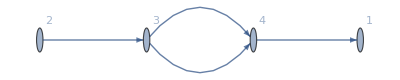
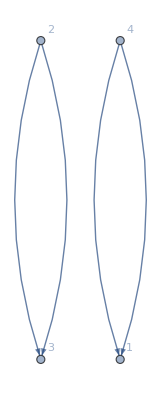
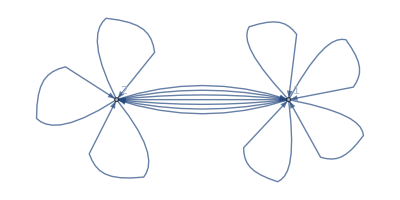
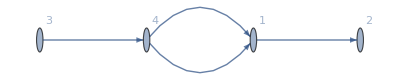
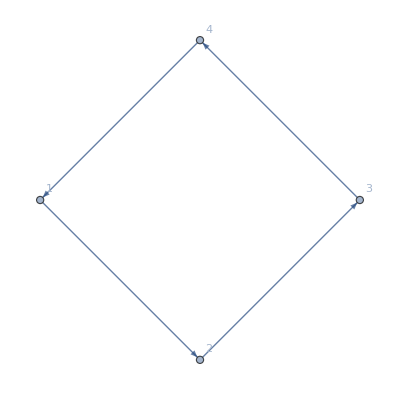
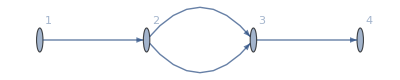
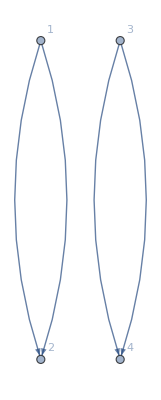
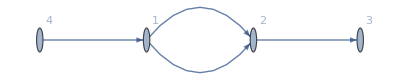
{{{1,4},Graph[{3→4,3→4,4→1,4→1},DirectedEdges→True,VertexLabels→{1→1,2→2,3→3,4→4}],{}},{{1,5},-Graphics-,{}},{{1,6},-Graphics-,{}},{{1,7},-Graphics-,{}},{{1,8},Graph[{2→3,2→3,3→4,3→4},DirectedEdges→True,VertexLabels→{1→1,2→2,3→3,4→4}],{}},{{2,3},-Graphics-,{}},{{2,4},-Graphics-,{}},{{2,5},-Graphics-,{{{1,2,3,4},4}}},{{2,6},-Graphics-,{{{1,2,3,4},4}}},{{2,8},-Graphics-,{}},{{3,4},-Graphics-,{}},{{3,5},-Graphics-,{{{1,2,3,4},4}}},{{3,6},-Graphics-,{{{1,2,3,4},4}}},{{3,8},-Graphics-,{}},{{4,7},Graph[{1→2,1→2,4→1,4→1},DirectedEdges→True,VertexLabels→{1→1,2→2,3→3,4→4}],{}},{{4,8},-Graphics-,{}},{{5,6},-Graphics-,{}},{{5,7},-Graphics-,{}},{{6,7},-Graphics-,{}},{{7,8},Graph[{1→2,1→2,2→3,2→3},DirectedEdges→True,VertexLabels→{1→1,2→2,3→3,4→4}],{}}}

```mathematica
Table[hMat2=Delete[hMat,Perf[[LiDoubleCuts[[i,1]]]]];
hMat3=Delete[hMat2,Perf[[LiDoubleCuts[[i,2]]]]];{LiDoubleCuts[[i]],PlotQuiver[hMat3],ListLoopRCharges[HeightMatrixToDSZ[hMat3],HeightMatrixToDSZ[hMat3]]},{i,Length[LiDoubleCuts]}]
```

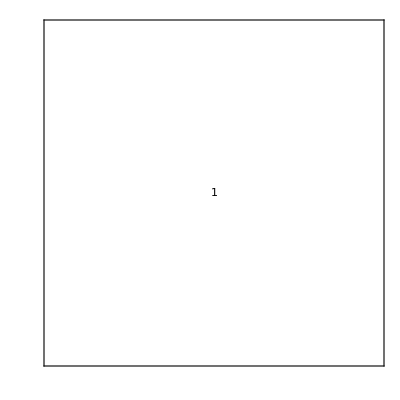
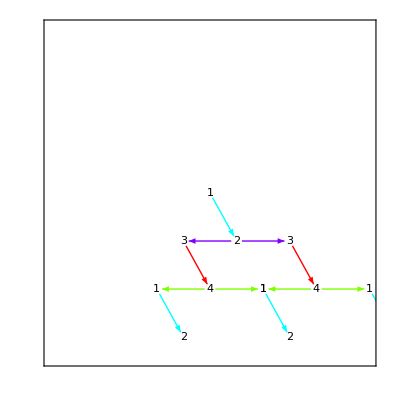
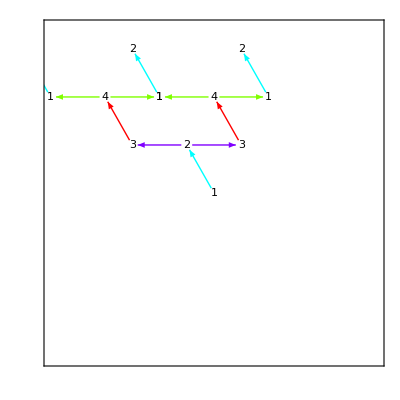
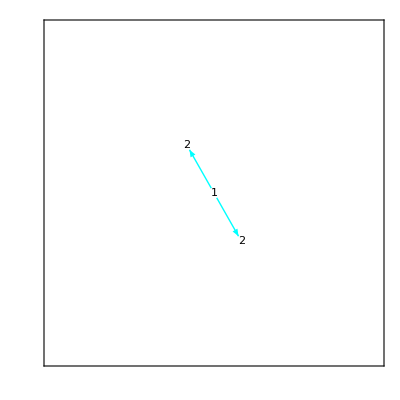
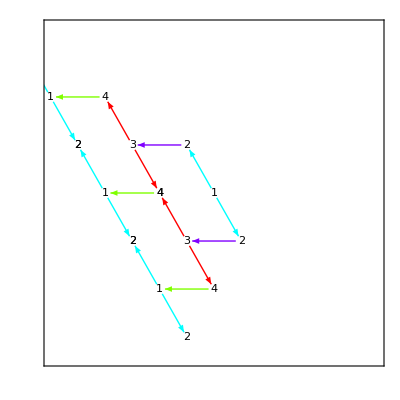
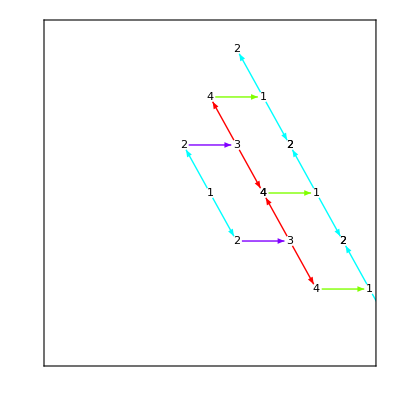
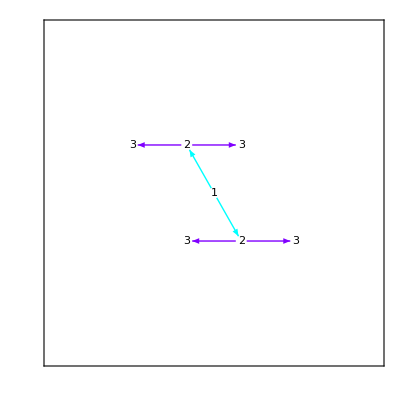
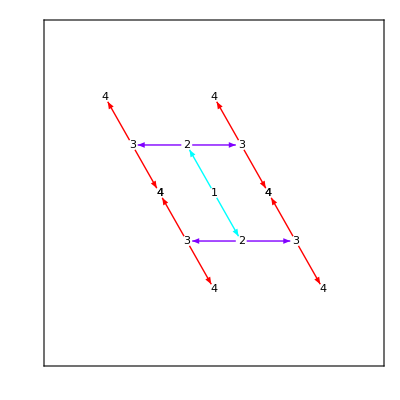
{{{{1,2,1},{1,2,2}},-Graphics-,-Graphics3D-},{{{1,2,1},{3,4,1}},-Graphics-,-Graphics3D-},{{{1,2,2},{3,4,2}},-Graphics-,-Graphics3D-},{{{2,3,1},{2,3,2}},-Graphics-,-Graphics3D-},{{{2,3,1},{4,1,1}},-Graphics-,-Graphics3D-},{{{2,3,2},{4,1,2}},-Graphics-,-Graphics3D-},{{{3,4,1},{3,4,2}},-Graphics-,-Graphics3D-},{{{4,1,1},{4,1,2}},-Graphics-,-Graphics3D-}}

```mathematica
Table[{Perf[[i]],
PlotTiling[hMat,5,{v1,v2},{{-3,3},{-3,3}},.1,Perf[[i]]],PlotTiling3D[hMat,5,{{1,0,0},{0,1,0},{0,0,1}},{{-3,3},{-3,3},{-3,3}},Perf[[i]]]}
,{i,Length[Perf]}]
```